## Finding the correlation of B and G channels :

### LacZ-tetherable:

```mathematica
myFileName  = FileNames["/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_aRCK_PBstain/20190223_TL_bl_aRCK_fix/AVG*"]
```

{/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_aRCK_PBstain/20190223_TL_bl_aRCK_fix/AVG_MAX_TLaRCK07.tif}

```mathematica
myFile = Import[myFileName[[1]]];
```

```mathematica
myMask = -Graphics-;
```

```mathematica
myCellImg =  myFile*myMask;
```

```mathematica
myImgPixels = Transpose[Table[Flatten@ImageData[myCellImg[[i]] ],{i,1,Length@myCellImg}]  ]//DeleteCases[#,{0.,0.,0.}]&;
```

```mathematica
myImgPixels//Dimensions
myImgPixels[[1]]
(*512^2
```

{45081,3}

{0.0164645,0.0340276,0.0243992}

```mathematica
Graphics[{ Opacity[.25],Circle[{0,0},1] } ]
```

-Graphics-

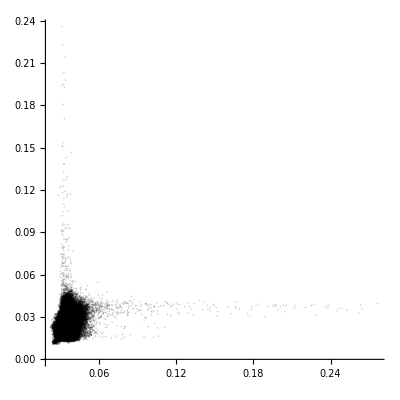

```mathematica
a = ListPlot[{myImgPixels[[All,2;;3]]  },PlotRange->All, PlotStyle->Opacity[0.2,Black],  AspectRatio->1]
```

```mathematica
a = ListPlot[{myImgPixels[[1;;All;;5,2;;3]]  },PlotRange->All, PlotStyle->Black, PlotMarkers->{-Graphics-, .025 }, AspectRatio->1]
```

### AGO2-tetherable:

```mathematica
myFileName  = FileNames["/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_aRCK_PBstain/20190222_TA_bl_aRCK_fix/AVG*"]
```

{/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_aRCK_PBstain/20190222_TA_bl_aRCK_fix/AVG_MAX_TAaRCK03.tif}

```mathematica
myFile = Import[myFileName[[1]]];
```

```mathematica
myFile//ColorCombine//ImageAdjust
```

```mathematica
myMask = -Graphics-;
```

```mathematica
myCellImg =  myFile*myMask;
```

```mathematica
myImgPixels = Transpose[Table[Flatten@ImageData[myCellImg[[i]] ],{i,1,Length@myCellImg}]  ]//DeleteCases[#,{0.,0.,0.}]&;
```

```mathematica
myImgPixels//Dimensions
myImgPixels[[1]]
(*512^2
```

{40823,3}

{0.0151827,0.0177157,0.0112306}

```mathematica
Graphics[{ Opacity[.25],Circle[{0,0},1] } ]
```

-Graphics-

```mathematica
a = ListPlot[{myImgPixels[[1;;All;;5,2;;3]]  },PlotRange->All, PlotStyle-> Black,PlotMarkers->{-Graphics-, .025 }, AspectRatio->1]
```

$Aborted

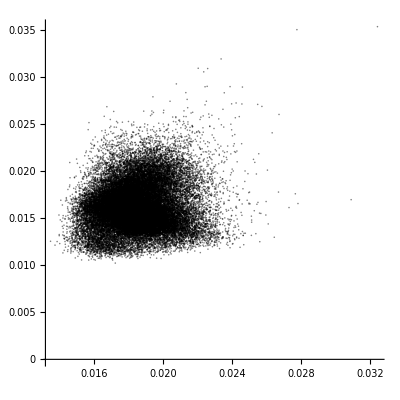

```mathematica
ListPlot[{myImgPixels[[All,2;;3]]  },PlotRange->All, PlotStyle->Opacity[0.5,Black],  ScalingFunctions->"Linear",AspectRatio->1]
```

### Non-tetherable:

```mathematica
myFileName  = FileNames["/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_aRCK_PBstain/20190226*/AVG*01*"]
```

{/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_aRCK_PBstain/20190226_NT_BL_beadload_fix_aRCK/AVG_MAX_NT15h01_laser647only.tif}

```mathematica
myFile = Import[myFileName[[1]]];
```

```mathematica
myFile//ColorCombine//ImageAdjust
```

```mathematica
myMask =-Graphics- ;
```

```mathematica
myCellImg =  myFile*myMask;
```

```mathematica
myImgPixels = Transpose[Table[Flatten@ImageData[myCellImg[[i]] ],{i,1,Length@myCellImg}]  ]//DeleteCases[#,{0.,0.,0.}]&;
```

```mathematica
myImgPixels//Dimensions
myImgPixels[[1]]
(*512^2
```

{28254,3}

{0.00972,0.0254368,0.0135042}

```mathematica
Graphics[{ Opacity[.25],Circle[{0,0},1] } ]
```

-Graphics-

```mathematica
a = ListPlot[{myImgPixels[[All,2;;3]]  },PlotRange->All, PlotStyle->Opacity[0.5,Black],  AspectRatio->1]
```

```mathematica
a = ListPlot[{myImgPixels[[1;;All;;5,2;;3]]  },PlotRange->All, PlotStyle->Black, PlotMarkers->{-Graphics-, .025 }, AspectRatio->1]
```

$Aborted